```mathematica
$Assumptions = {J ∈ Reals, x ∈ Reals, y ∈ Reals, θ ∈ Reals, q ∈ Reals, M ∈ Reals, δ ∈ Reals, δ > 0}
```

{J∈ℝ,x∈ℝ,y∈ℝ,θ∈ℝ,q∈ℝ,M∈ℝ,δ∈ℝ,δ>0}

```mathematica
ω = Exp[I 2 π/3];
Δ1 = 0;
Δ3 = -δ;
Δ5 = δ;
Δt = 1/2(Δ1 - Δ5);
q0=δ/J Sqrt[2];
θ=ArcTan[x,y];
q=Sqrt[x^2+y^2];
```

## Matrices

```mathematica
H0 = FullSimplify[(Δ3 - (Δ5 + Δt) + Sqrt[Δt^2 + J^2 q^2])/2]
dVx = FullSimplify[(M q Cos[θ] (Δt + Sqrt[Δt^2+J^2 q^2]))/Sqrt[2 J^2 q^2 + 2 Δt^2 + 2 Δt Sqrt[Δt^2 + J^2 q^2]]]
dVy = FullSimplify[(M q Sin[θ] (Δt + Sqrt[Δt^2+J^2 q^2]))/Sqrt[2 J^2 q^2 + 2 Δt^2 + 2 Δt Sqrt[Δt^2 + J^2 q^2]]]
```

1/4 (-3 δ+√(4 J^2 (x^2+y^2)+δ^2))

(M x (-δ+√(4 J^2 (x^2+y^2)+δ^2)))/(√(8 J^2 (x^2+y^2)+2 δ (δ-√(4 J^2 (x^2+y^2)+δ^2))))

(M y (-δ+√(4 J^2 (x^2+y^2)+δ^2)))/(√(8 J^2 (x^2+y^2)+2 δ (δ-√(4 J^2 (x^2+y^2)+δ^2))))

```mathematica
mag = FullSimplify[H0^2+dVx^2+dVy^2]
```

1/(8 √(4 J^2 (x^2+y^2)+δ^2))(2 J^2 (x^2+y^2) (-6 δ+√(4 J^2 (x^2+y^2)+δ^2))+4 M^2 (x^2+y^2) (-δ+√(4 J^2 (x^2+y^2)+δ^2))+δ^2 (-3 δ+5 √(4 J^2 (x^2+y^2)+δ^2)))

## Shifted Minima

```mathematica
mag0 = FullSimplify[mag];
magx = FullSimplify[D[mag,x]];
magy = FullSimplify[D[mag,y]];
```

```mathematica
x=q0;
y=0;
FullSimplify[mag0]
FullSimplify[magx]
FullSimplify[magy]
```

(2 M^2 δ^2)/(3 J^2)

(22 √2 M^2 δ)/(27 J)

0

```mathematica
Clear[x,y];
cond = FullSimplify[(2 M^2 δ^2)/(3 J^2) + (22 √2 M^2 δ)/(27 J) (x-q0)]
```

(2 M^2 (11 √2 J x-13 δ) δ)/(27 J^2)

```mathematica
x0= FullSimplify[1/((22 √2 M^2 δ)/(27 J)) * (q0 * (22 √2 M^2 δ)/(27 J) - (2 M^2 δ^2)/(3 J^2))]
y0 =0
```

(13 δ)/(11 √2 J)

0

```mathematica
FullSimplify[x0]
```

0.172313

```mathematica
FullSimplify[q0]
```

0.291606

## Un-perturbed Hamiltonian

```mathematica
H00=FullSimplify[H0];
H0x=FullSimplify[D[H0,x]];
H0y=FullSimplify[D[H0,y]];
```

```mathematica
x=x0;
y=y0;
FullSimplify[H00]
FullSimplify[H0x]
FullSimplify[H0y]
```

3/44 (-11+√51) δ

(13 J)/(3 √102)

0

```mathematica
Clear[x,y];
approxH0 = FullSimplify[3/44 (-11+√51) δ + (13 J)/(3 √102) (x - x0)]
```

1/612 (26 √102 J x+(-459+11 √51) δ)

## Perturbation

```mathematica
Vx0 = FullSimplify[dVx];
Vxx = FullSimplify[D[dVx, x]];
Vxy = FullSimplify[D[dVx, y]];
Vy0 = FullSimplify[dVy];
Vyx = FullSimplify[D[dVy, x]];
Vyy = FullSimplify[D[dVy, y]];
```

```mathematica
x=x0;
y=y0;
FullSimplify[Vx0]
FullSimplify[Vxx]
FullSimplify[Vxy]
```

(13 √(9-11 √(3/17)) M δ)/(66 J)

(√(3976299-996919 √(3/17)) M)/2754

0

```mathematica
Clear[x,y];
approxVx = FullSimplify[(13 √(9-11 √(3/17)) M δ)/(66 J) + (√(3976299-996919 √(3/17)) M)/2754 (x-x0)]
```

(2 √(17 (67597083-996919 √51)) J M x-169 √(5202+374 √51) M δ)/(93636 J)

```mathematica
x=x0;
y=y0;
FullSimplify[Vy0]
FullSimplify[Vyx]
FullSimplify[Vyy]
```

0

0

M Root0.493Root[169-918 #1^2+918 #1^4&,3]0.49323623609267075

```mathematica
Clear[x,y];
approxVy = FullSimplify[M/(√3) y]
```

(M y)/(√3)

## Berry Curvature

```mathematica
dx = FullSimplify[approxVx];
dy = FullSimplify[approxVy];
dz = FullSimplify[approxH0];
d = FullSimplify[{dx, dy, dz}]
```

{(M (11 J x-2 √2 δ))/(9 √3 J),(M y)/(√3),1/3 (√2 J x-2 δ)}

```mathematica
Ω = FullSimplify[ComplexExpand[(d.Cross[D[d, x], D[d, y]])/(2 Norm[d]^3)]]
```

-(243 √3 M^2 δ)/((81 M^2 y^2+27 (√2 J x-2 δ)^2+(M^2 (11 J x-2 √2 δ)^2)/J^2)^(3/2))

```mathematica
J=2.1
M=0.15
δ=0.4330127018922193
y=0
(*FullSimplify[Ω]*)
```

2.1

0.15

0.433013

0

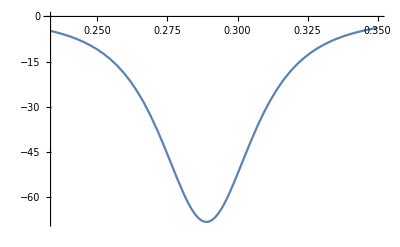

```mathematica
Plot[Ω, {x, 0.8*q0, 1.2*q0}]
```

## Another attempt

```mathematica
(*dVx = FullSimplify[(M J q^2 Cos[2 θ])/Sqrt[2 J^2 q^2 + 2 Δt^2 + 2 Δt Sqrt[Δt^2 + J^2 q^2]]];
dVy = FullSimplify[(M J q^2 Sin[2 θ])/Sqrt[2 J^2 q^2 + 2 Δt^2 + 2 Δt Sqrt[Δt^2 + J^2 q^2]]];*)
```

```mathematica
(*Vx0 = FullSimplify[dVx];
Vxx = FullSimplify[D[dVx, x]];
Vxy = FullSimplify[D[dVx, y]];
Vy0 = FullSimplify[dVy];
Vyx = FullSimplify[D[dVy, x]];
Vyy = FullSimplify[D[dVy, y]];*)
```

```mathematica
(*x=q0;
y=0;
FullSimplify[Vx0]
FullSimplify[Vxx]
FullSimplify[Vxy]*)
```

(2 M δ)/(√3 J)

8/9 √(2/3) M

0

```mathematica
(*Clear[x,y];
approxVx = FullSimplify[(2 M δ)/(√3 J)+8/9 √(2/3) M (x-q0)]*)
```

(2 M (4 √2 J x+δ))/(9 √3 J)

```mathematica
(*x=q0;
y=0;
FullSimplify[Vy0]
FullSimplify[Vyx]
FullSimplify[Vyy]*)
```

0

0

2 √(2/3) M

```mathematica
(*Clear[x,y];
approxVy = FullSimplify[2 √(2/3) M y]*)
```

2 √(2/3) M y